## Prepare

```mathematica
imgsize=700;
imgpadding={{70, 20}, {50, 10}};
```

## Solving Eqns

I use x̄=omega x as variable x here. In other words, the x I am going to use is in fact omega x.

```mathematica
ClearAll[sin2thetav,α0,α1,β,θ]
```

```mathematica
eqn1= I c1'[x]==Cos[2θ]/2(α0+α1 Cos[β x])c1[x]+Sin[2θ]/2(α0+α1 Cos[β x])c2[x]Exp[-I x]
eqn2=I c2'[x]==-Cos[2θ]/2(α0+α1 Cos[β x])c2[x]+ Sin[2θ]/2(α0+α1 Cos[β x])c1[x] Exp[I x]
```

ⅈ c1'[x]==1/2 c1[x] (α0+α1 Cos[x β]) Cos[2 θ]+1/2 ⅇ^(-ⅈ x) c2[x] (α0+α1 Cos[x β]) Sin[2 θ]

ⅈ c2'[x]==-1/2 c2[x] (α0+α1 Cos[x β]) Cos[2 θ]+1/2 ⅇ^(ⅈ x) c1[x] (α0+α1 Cos[x β]) Sin[2 θ]

```mathematica
init1=c1[0]==1
init2=c2[0]==0
```

c1[0]==1

c2[0]==0

```mathematica
solana=DSolve[{eqn1,eqn2,init1,init2},{c1,c2},x]
```

DSolve[{ⅈ c1'[x]==1/2 c1[x] (α0+α1 Cos[x β]) Cos[2 θ]+1/2 ⅇ^(-ⅈ x) c2[x] (α0+α1 Cos[x β]) Sin[2 θ],ⅈ c2'[x]==-1/2 c2[x] (α0+α1 Cos[x β]) Cos[2 θ]+1/2 ⅇ^(ⅈ x) c1[x] (α0+α1 Cos[x β]) Sin[2 θ],c1[0]==1,c2[0]==0},{c1,c2},x]

The parameters to be used

```mathematica
sin2thetav=0.917;
α0=0.1;
α1=0;
β=0.1;
θ=ArcSin[sin2thetav]/2;
```

```mathematica
endpoint=800
```

800

```mathematica
solnum=NDSolve[{eqn1,eqn2,init1,init2},{c1,c2},{x,0,endpoint}]
```

{{c1→InterpolatingFunction[{{0., 800.}}, <>],c2→InterpolatingFunction[{{0., 800.}}, <>]}}

```mathematica
solnum[[1]]
```

{c1→InterpolatingFunction[{{0., 800.}}, <>],c2→InterpolatingFunction[{{0., 800.}}, <>]}

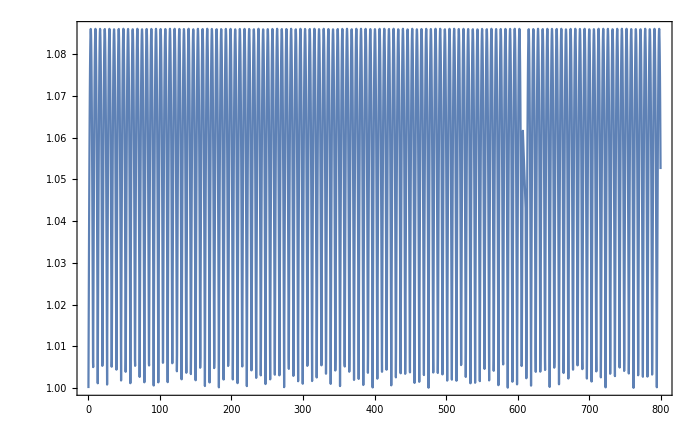

```mathematica
normnum=Plot[Evaluate[Abs[c1[x]]^2+Abs[c2[x]]/.solnum[[1]]],{x,0,endpoint},PlotRange->All,ImageSize->imgsize,Frame->True]
```

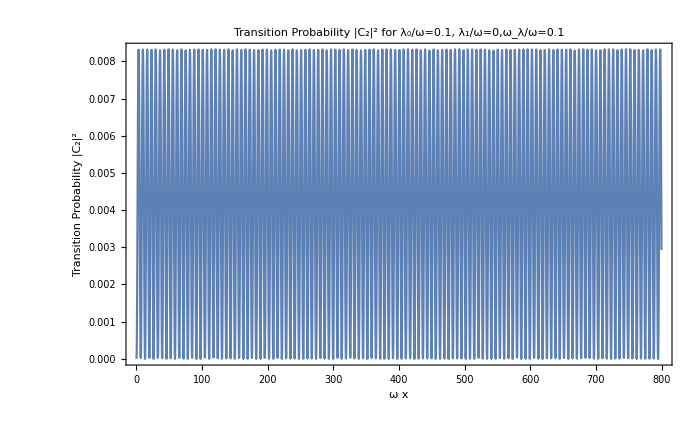

```mathematica
numP=Plot[Evaluate[Abs[c2[x]]^2/(Abs[c1[x]]^2+Abs[c2[x]])/.solnum[[1]]],{x,0,endpoint},PlotRange->All,PlotLabel->"Transition Probability |C_2|^2 for λ_0/ω=0.1, λ_1/ω=0,ω_λ/ω=0.1",ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Transition Probability |C_2|^2"},ImagePadding->imgpadding]
```

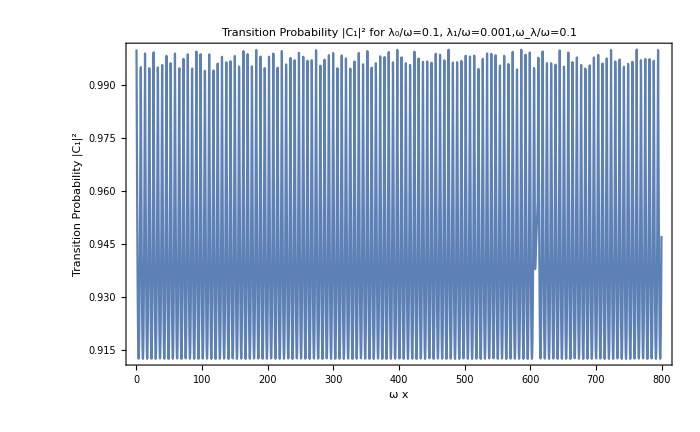

```mathematica
numP1=Plot[Evaluate[Abs[c1[x]]^2/(Abs[c1[x]]^2+Abs[c2[x]])/.solnum[[1]]],{x,0,endpoint},PlotRange->All,PlotLabel->"Transition Probability |C_1|^2 for λ_0/ω=0.1, λ_1/ω=0.001,ω_λ/ω=0.1",ImageSize->imgsize,Frame->True,FrameLabel->{"ω x","Transition Probability |C_1|^2"},ImagePadding->imgpadding]
```